{InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t]}

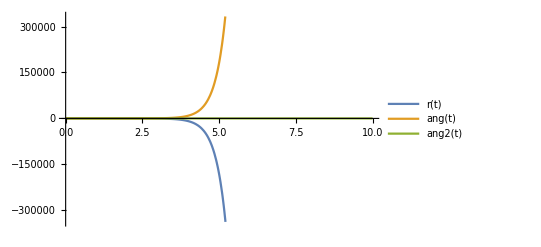

```mathematica
a:=1
A:=1
M:=1
i1:=1
omega:=1
g:=1
alpha:=0
beta:=0
{r[t_],ang[t_],ang2[t_]}=Values[First[NDSolve[{
epsilon''[t]==-3*A*Sin[beta]*theta2[t]-9*A*Cos[alpha]*theta[t]+g/a,
theta''[t]==3*A*Cos[alpha]*(1-3*epsilon[t]),
theta2''[t]==A*a^2*M*Sin[beta]*(1-3*epsilon[t])/i1,
epsilon[0]==0,theta[0]==0,theta2[0]==0,epsilon'[0]==0,theta'[0]==0,theta2'[0]==0},
{epsilon[t],theta[t],theta2[t]},{t,0,10}]]]
Plot[{r[t],ang[t],ang2[t]},{t,0,10},PlotLegends->"Expressions"]
```